# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\Poh\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.03.1\\bin\\gswin64c.exe"
]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Poh\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.03.1\bin\gswin64c.exe}

```mathematica
Needs["MaTeX`"]
```

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]);
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
factgeom[1,30.2,10,10]
```

0.107827

```mathematica
(*COMPROBANDO FUNCIONAMIENTO DE LOS FACTORES PARA OBLATO Y PROLATO*)
```

```mathematica
L1[a_,b_]:=Module[{eab2=1-(b^2/a^2),L1},L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])])]
L11[a_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1},L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2)]
```

```mathematica
hola=Table[{Sqrt[1-(c^2/10^2)],L11[10,c]},{c,0.001,10,0.01}];
hola2=Table[{Sqrt[1-(b^2/10^2)],L1[10,b]},{b,0.001,10,0.01}];
```

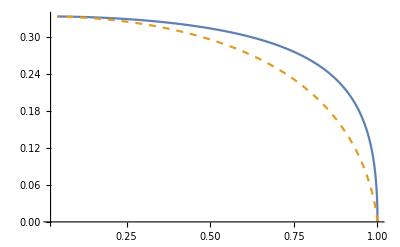

```mathematica
ListLinePlot[{hola,Style[hola2,Dashed]},PlotRange->All]
```

## Definiciones

### Función dieléctrica de tipo Drude

Definiendo la sección transversal de absorción

```mathematica
Cabs[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Csca[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αx]^2/(6 Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cext[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[1]]+Cabs[a,b,c,nm,λ,λp,γ][[1]]
Cextx[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[2]]+Cabs[a,b,c,nm,λ,λp,γ][[2]]
Cextz[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[3]]+Cabs[a,b,c,nm,λ,λp,γ][[3]]
```

### Datos experimentales

```mathematica
Cabsexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2αx+ αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Cscaexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+ αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cextexp[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[1]]+Cabsexp[a,b,c,nm,λ,np][[1]]
Cextexpx[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[2]]+Cabsexp[a,b,c,nm,λ,np][[2]]
Cextexpz[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[3]]+Cabsexp[a,b,c,nm,λ,np][[3]]
```

```mathematica
Cextexp[30,10,10,1.33,144,1]
```

66.7352

## Cálculos

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
h vlight/300
```

4.13567

Se graficará la Cext promedio contrastada con las Cext individuales

```mathematica
qextAlDrpromedio=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
qextAlDrx=Table[{h vlight/λ,Cextx[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
qextAlDrz=Table[{h vlight/λ,Cextz[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
qextAlSphe=Table[{h vlight/λ,Cextz[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
```

```mathematica
h vlight/6
```

206.783

```mathematica
upperTicksCext=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];

upperTicksMinorCext=Module[{labels,positions,size},labels={3.5,4.2,4.6,6,8,9,12,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

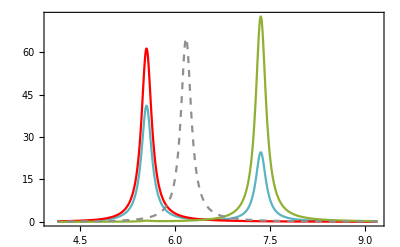

```mathematica
cextAl=ListLinePlot[{Style[qextAlDrpromedio,RGBColor[0.349,0.71,0.749]],Style[qextAlDrx,Red],Style[qextAlDrz,RGBColor[0.560181,0.691569,0.194885]],Style[qextAlSphe,Dashed,RGBColor[0.561,0.561,0.561]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.2]&/@{MaTeX["\langle C_{ext}"],MaTeX["C_{ext}^{(1)}"],MaTeX["C_{ext}^{(3)}"],MaTeX["\langle C_{ext}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.8,0.70}]]
```

```mathematica
Export["CextAlbueno.svg",cextAl]
```

CextAlbueno.svg

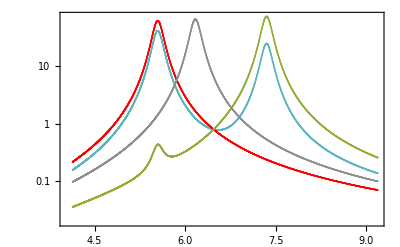

```mathematica
cextAl=ListLogPlot[{Style[qextAlDrpromedio,RGBColor[0.349,0.71,0.749]],Style[qextAlDrx,Red],Style[qextAlDrz,RGBColor[0.560181,0.691569,0.194885]],Style[qextAlSphe,Dashed,RGBColor[0.561,0.561,0.561]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.2]&/@{MaTeX["\langle C_{ext}"],MaTeX["C_{ext}^{(1)}"],MaTeX["C_{ext}^{(3)}"],MaTeX["\langle C_{ext}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.87,0.73}]]
```

```mathematica
Export["CextAlbueno.svg",cextAl]
```

CextAlbueno.svg

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAlDr=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.05}];
qextAl1Dr=Table[{h vlight/λ,Cext[1.75,1.75,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.05}];
qextAl2Dr=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl3Dr=Table[{h vlight/λ,Cext[2.25,2.25,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];qextEsferaDr=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
```

```mathematica
qextEsferaDr=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350}]
```

```mathematica
upperTicksAl=Module[{labels,positions},labels={124,138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

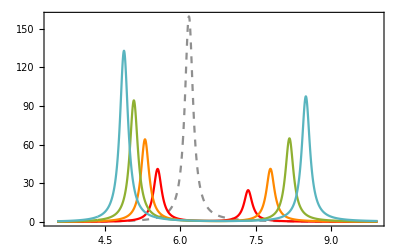

```mathematica
alc=ListLinePlot[{Style[qextEsferaDr,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlDr,Red],Style[qextAl1Dr,RGBColor[1,0.533,0]],Style[qextAl2Dr,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3Dr,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",3},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.1]],{0.75,0.8}]]
```

```mathematica
Export["Alc.png",alc]
```

Alc.png

#### Misma razón de aspecto

```mathematica
qextAlAR=Table[{h vlight/λ,Cext[1.0,1.0,0.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl1AR=Table[{h vlight/λ,Cext[1.5,1.5,0.75,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl2AR=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl3AR=Table[{h vlight/λ,Cext[2.5,2.5,1.25,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl3sphere=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
```

```mathematica
qextAl3sphere=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.1}]
```

{{9.54385,0.220025},{9.53651,0.220782},{9.52919,0.221543},{9.52187,0.222308},{9.51457,0.223076},{9.50728,0.223847},{9.5,0.224622},{9.49273,0.225401},{9.48548,0.226183},{9.47823,0.226969},{9.47099,0.227758},{9.46377,0.228551},{9.45656,0.229348},{9.44935,0.230149},{9.44216,0.230953},{9.43498,0.231761},{9.42781,0.232573},{9.42066,0.233389},{9.41351,0.234208},{9.40637,0.235031},{9.39924,0.235859},{9.39213,0.23669},{9.38503,0.237525},{9.37793,0.238363},{9.37085,0.239206},{9.36378,0.240053},{9.35671,0.240904},{9.34966,0.241759},{9.34262,0.242618},{9.33559,0.243481},{9.32857,0.244348},{9.32157,0.245219},{9.31457,0.246094},{9.30758,0.246974},{9.3006,0.247858},{9.29364,0.248745},{9.28668,0.249638},{9.27973,0.250534},{9.2728,0.251435},{9.26587,0.25234},{9.25896,0.25325},{9.25205,0.254163},{9.24516,0.255082},{9.23827,0.256004},{9.2314,0.256931},{9.22454,0.257863},{9.21768,0.258799},{9.21084,0.25974},{9.20401,0.260685},{9.19719,0.261635},{9.19037,0.26259},{9.18357,0.263549},{9.17678,0.264513},{9.16999,0.265481},{9.16322,0.266454},{9.15646,0.267432},{9.14971,0.268415},{9.14296,0.269403},{9.13623,0.270396},{9.12951,0.271393},{9.1228,0.272395},{9.11609,0.273403},{9.1094,0.274415},{9.10272,0.275432},{9.09604,0.276455},{9.08938,0.277482},{9.08273,0.278515},{9.07608,0.279552},{9.06945,0.280595},{9.06282,0.281643},{9.05621,0.282697},{9.0496,0.283755},{9.04301,0.284819},{9.03642,0.285888},{9.02984,0.286963},{9.02327,0.288043},{9.01672,0.289129},{9.01017,0.29022},{9.00363,0.291316},{8.9971,0.292418},{8.99058,0.293526},{8.98407,0.294639},{8.97757,0.295758},{8.97108,0.296882},{8.9646,0.298013},{8.95812,0.299149},{8.95166,0.300291},{8.94521,0.301438},{8.93876,0.302592},{8.93233,0.303752},{8.9259,0.304917},{8.91948,0.306089},{8.91308,0.307266},{8.90668,0.30845},{8.90029,0.30964},{8.89391,0.310835},{8.88754,0.312038},{8.88118,0.313246},{8.87482,0.314461},{8.86848,0.315681},{8.86215,0.316909},{8.85582,0.318143},{8.8495,0.319383},{8.8432,0.320629},{8.8369,0.321883},{8.83061,0.323142},{8.82433,0.324409},{8.81805,0.325682},{8.81179,0.326962},{8.80554,0.328248},{8.79929,0.329542},{8.79306,0.330842},{8.78683,0.332149},{8.78061,0.333463},{8.7744,0.334784},{8.7682,0.336112},{8.76201,0.337448},{8.75582,0.33879},{8.74965,0.340139},{8.74348,0.341496},{8.73733,0.34286},{8.73118,0.344232},{8.72504,0.34561},{8.71891,0.346997},{8.71278,0.34839},{8.70667,0.349792},{8.70056,0.3512},{8.69447,0.352617},{8.68838,0.354041},{8.6823,0.355473},{8.67623,0.356913},{8.67016,0.35836},{8.66411,0.359816},{8.65806,0.361279},{8.65202,0.362751},{8.646,0.364231},{8.63997,0.365718},{8.63396,0.367214},{8.62796,0.368719},{8.62196,0.370231},{8.61597,0.371752},{8.61,0.373281},{8.60402,0.374819},{8.59806,0.376366},{8.59211,0.377921},{8.58616,0.379485},{8.58022,0.381057},{8.57429,0.382638},{8.56837,0.384228},{8.56246,0.385828},{8.55655,0.387436},{8.55066,0.389053},{8.54477,0.390679},{8.53889,0.392315},{8.53301,0.393959},{8.52715,0.395613},{8.52129,0.397277},{8.51544,0.39895},{8.5096,0.400632},{8.50377,0.402324},{8.49795,0.404026},{8.49213,0.405738},{8.48632,0.407459},{8.48052,0.40919},{8.47473,0.410932},{8.46894,0.412683},{8.46317,0.414444},{8.4574,0.416216},{8.45164,0.417998},{8.44588,0.41979},{8.44014,0.421592},{8.4344,0.423406},{8.42867,0.425229},{8.42295,0.427064},{8.41723,0.428909},{8.41153,0.430765},{8.40583,0.432632},{8.40014,0.434509},{8.39445,0.436398},{8.38878,0.438298},{8.38311,0.44021},{8.37745,0.442132},{8.3718,0.444066},{8.36615,0.446012},{8.36051,0.447969},{8.35488,0.449938},{8.34926,0.451919},{8.34365,0.453911},{8.33804,0.455916},{8.33244,0.457932},{8.32685,0.459961},{8.32126,0.462001},{8.31569,0.464055},{8.31012,0.46612},{8.30455,0.468198},{8.299,0.470289},{8.29345,0.472393},{8.28791,0.474509},{8.28238,0.476638},{8.27685,0.478781},{8.27134,0.480936},{8.26582,0.483105},{8.26032,0.485287},{8.25483,0.487482},{8.24934,0.489691},{8.24386,0.491914},{8.23838,0.49415},{8.23292,0.496401},{8.22746,0.498665},{8.222,0.500943},{8.21656,0.503236},{8.21112,0.505543},{8.20569,0.507865},{8.20027,0.510201},{8.19485,0.512551},{8.18944,0.514917},{8.18404,0.517297},{8.17864,0.519693},{8.17326,0.522104},{8.16788,0.52453},{8.1625,0.526971},{8.15714,0.529428},{8.15178,0.531901},{8.14642,0.53439},{8.14108,0.536894},{8.13574,0.539415},{8.13041,0.541951},{8.12508,0.544505},{8.11977,0.547074},{8.11446,0.54966},{8.10915,0.552263},{8.10386,0.554883},{8.09857,0.55752},{8.09328,0.560175},{8.08801,0.562846},{8.08274,0.565535},{8.07748,0.568242},{8.07222,0.570966},{8.06697,0.573709},{8.06173,0.576469},{8.0565,0.579248},{8.05127,0.582045},{8.04605,0.584861},{8.04083,0.587695},{8.03562,0.590549},{8.03042,0.593421},{8.02523,0.596313},{8.02004,0.599224},{8.01486,0.602155},{8.00969,0.605105},{8.00452,0.608075},{7.99936,0.611065},{7.9942,0.614076},{7.98906,0.617107},{7.98391,0.620159},{7.97878,0.623231},{7.97365,0.626324},{7.96853,0.629439},{7.96342,0.632575},{7.95831,0.635732},{7.95321,0.638912},{7.94811,0.642113},{7.94302,0.645336},{7.93794,0.648582},{7.93287,0.65185},{7.9278,0.655141},{7.92274,0.658455},{7.91768,0.661792},{7.91263,0.665152},{7.90759,0.668536},{7.90255,0.671944},{7.89752,0.675376},{7.8925,0.678832},{7.88748,0.682312},{7.88247,0.685817},{7.87746,0.689347},{7.87246,0.692903},{7.86747,0.696483},{7.86249,0.700089},{7.85751,0.703722},{7.85253,0.70738},{7.84757,0.711064},{7.84261,0.714775},{7.83765,0.718513},{7.8327,0.722278},{7.82776,0.726071},{7.82283,0.729891},{7.8179,0.733739},{7.81297,0.737615},{7.80806,0.741519},{7.80315,0.745452},{7.79824,0.749414},{7.79334,0.753406},{7.78845,0.757427},{7.78357,0.761477},{7.77869,0.765558},{7.77381,0.769669},{7.76894,0.773811},{7.76408,0.777984},{7.75923,0.782188},{7.75438,0.786423},{7.74953,0.790691},{7.7447,0.794991},{7.73986,0.799323},{7.73504,0.803688},{7.73022,0.808087},{7.72541,0.812519},{7.7206,0.816984},{7.7158,0.821484},{7.711,0.826019},{7.70621,0.830588},{7.70143,0.835192},{7.69665,0.839833},{7.69188,0.844509},{7.68711,0.849221},{7.68235,0.85397},{7.6776,0.858756},{7.67285,0.86358},{7.66811,0.868441},{7.66337,0.87334},{7.65864,0.878279},{7.65392,0.883256},{7.6492,0.888272},{7.64449,0.893328},{7.63978,0.898425},{7.63508,0.903562},{7.63038,0.90874},{7.62569,0.91396},{7.62101,0.919222},{7.61633,0.924525},{7.61166,0.929872},{7.60699,0.935262},{7.60233,0.940696},{7.59767,0.946174},{7.59303,0.951697},{7.58838,0.957264},{7.58374,0.962878},{7.57911,0.968537},{7.57448,0.974243},{7.56986,0.979997},{7.56525,0.985797},{7.56064,0.991646},{7.55603,0.997544},{7.55143,1.00349},{7.54684,1.00949},{7.54225,1.01553},{7.53767,1.02163},{7.53309,1.02778},{7.52852,1.03398},{7.52396,1.04024},{7.5194,1.04654},{7.51484,1.0529},{7.51029,1.05932},{7.50575,1.06579},{7.50121,1.07231},{7.49668,1.07889},{7.49215,1.08553},{7.48763,1.09223},{7.48311,1.09898},{7.4786,1.10579},{7.4741,1.11266},{7.4696,1.1196},{7.4651,1.12659},{7.46062,1.13364},{7.45613,1.14076},{7.45165,1.14794},{7.44718,1.15518},{7.44271,1.16249},{7.43825,1.16986},{7.43379,1.1773},{7.42934,1.18481},{7.4249,1.19238},{7.42046,1.20002},{7.41602,1.20773},{7.41159,1.21551},{7.40717,1.22336},{7.40275,1.23128},{7.39833,1.23928},{7.39392,1.24734},{7.38952,1.25549},{7.38512,1.2637},{7.38073,1.272},{7.37634,1.28037},{7.37196,1.28881},{7.36758,1.29734},{7.36321,1.30595},{7.35884,1.31463},{7.35448,1.3234},{7.35012,1.33225},{7.34577,1.34119},{7.34142,1.35021},{7.33708,1.35932},{7.33274,1.36851},{7.32841,1.37779},{7.32409,1.38716},{7.31977,1.39662},{7.31545,1.40617},{7.31114,1.41582},{7.30683,1.42556},{7.30253,1.43539},{7.29824,1.44532},{7.29395,1.45535},{7.28966,1.46547},{7.28538,1.4757},{7.28111,1.48603},{7.27683,1.49645},{7.27257,1.50699},{7.26831,1.51763},{7.26405,1.52837},{7.2598,1.53923},{7.25556,1.55019},{7.25132,1.56126},{7.24708,1.57245},{7.24285,1.58375},{7.23862,1.59516},{7.2344,1.6067},{7.23019,1.61835},{7.22598,1.63012},{7.22177,1.64201},{7.21757,1.65403},{7.21337,1.66617},{7.20918,1.67844},{7.205,1.69084},{7.20081,1.70336},{7.19664,1.71602},{7.19247,1.72882},{7.1883,1.74175},{7.18414,1.75482},{7.17998,1.76802},{7.17583,1.78137},{7.17168,1.79487},{7.16754,1.8085},{7.1634,1.82229},{7.15926,1.83623},{7.15513,1.85032},{7.15101,1.86456},{7.14689,1.87896},{7.14278,1.89352},{7.13867,1.90823},{7.13456,1.92312},{7.13046,1.93817},{7.12637,1.95338},{7.12228,1.96877},{7.11819,1.98433},{7.11411,2.00007},{7.11003,2.01598},{7.10596,2.03208},{7.10189,2.04836},{7.09783,2.06482},{7.09377,2.08148},{7.08972,2.09832},{7.08567,2.11537},{7.08162,2.13261},{7.07758,2.15005},{7.07355,2.1677},{7.06952,2.18555},{7.06549,2.20361},{7.06147,2.22189},{7.05745,2.24039},{7.05344,2.2591},{7.04943,2.27804},{7.04543,2.29721},{7.04143,2.31661},{7.03744,2.33625},{7.03345,2.35612},{7.02946,2.37623},{7.02548,2.39659},{7.02151,2.41721},{7.01754,2.43807},{7.01357,2.4592},{7.00961,2.48058},{7.00565,2.50224},{7.00169,2.52416},{6.99775,2.54637},{6.9938,2.56885},{6.98986,2.59162},{6.98593,2.61467},{6.98199,2.63803},{6.97807,2.66168},{6.97414,2.68564},{6.97023,2.7099},{6.96631,2.73449},{6.9624,2.75939},{6.9585,2.78462},{6.9546,2.81018},{6.9507,2.83608},{6.94681,2.86232},{6.94292,2.88891},{6.93904,2.91586},{6.93516,2.94317},{6.93129,2.97085},{6.92742,2.9989},{6.92355,3.02733},{6.91969,3.05616},{6.91583,3.08537},{6.91198,3.11499},{6.90813,3.14502},{6.90429,3.17547},{6.90045,3.20634},{6.89661,3.23765},{6.89278,3.26939},{6.88895,3.30159},{6.88513,3.33424},{6.88131,3.36736},{6.8775,3.40095},{6.87369,3.43502},{6.86988,3.46959},{6.86608,3.50466},{6.86228,3.54025},{6.85849,3.57635},{6.8547,3.61298},{6.85091,3.65016},{6.84713,3.68789},{6.84336,3.72618},{6.83958,3.76505},{6.83581,3.8045},{6.83205,3.84455},{6.82829,3.88521},{6.82453,3.92649},{6.82078,3.96841},{6.81703,4.01097},{6.81329,4.05419},{6.80955,4.09809},{6.80582,4.14267},{6.80209,4.18795},{6.79836,4.23395},{6.79463,4.28068},{6.79092,4.32816},{6.7872,4.37639},{6.78349,4.42541},{6.77978,4.47522},{6.77608,4.52584},{6.77238,4.57729},{6.76869,4.62958},{6.765,4.68274},{6.76131,4.73679},{6.75763,4.79174},{6.75395,4.84761},{6.75027,4.90442},{6.7466,4.9622},{6.74294,5.02096},{6.73927,5.08073},{6.73562,5.14153},{6.73196,5.20339},{6.72831,5.26632},{6.72466,5.33036},{6.72102,5.39552},{6.71738,5.46184},{6.71375,5.52934},{6.71012,5.59804},{6.70649,5.66799},{6.70286,5.7392},{6.69925,5.8117},{6.69563,5.88554},{6.69202,5.96073},{6.68841,6.03732},{6.68481,6.11533},{6.68121,6.1948},{6.67761,6.27577},{6.67402,6.35828},{6.67043,6.44235},{6.66685,6.52804},{6.66327,6.61538},{6.65969,6.70441},{6.65612,6.79518},{6.65255,6.88773},{6.64898,6.9821},{6.64542,7.07835},{6.64186,7.17653},{6.63831,7.27668},{6.63476,7.37885},{6.63121,7.4831},{6.62767,7.58948},{6.62413,7.69806},{6.6206,7.80889},{6.61707,7.92203},{6.61354,8.03754},{6.61002,8.1555},{6.6065,8.27596},{6.60298,8.399},{6.59947,8.52468},{6.59596,8.6531},{6.59246,8.78431},{6.58896,8.9184},{6.58546,9.05546},{6.58196,9.19556},{6.57847,9.33881},{6.57499,9.48528},{6.57151,9.63507},{6.56803,9.78829},{6.56455,9.94503},{6.56108,10.1054},{6.55761,10.2695},{6.55415,10.4375},{6.55069,10.6094},{6.54723,10.7854},{6.54378,10.9657},{6.54033,11.1503},{6.53688,11.3393},{6.53344,11.533},{6.53,11.7315},{6.52657,11.9349},{6.52314,12.1434},{6.51971,12.3572},{6.51628,12.5764},{6.51286,12.8011},{6.50945,13.0317},{6.50603,13.2682},{6.50262,13.5109},{6.49922,13.76},{6.49581,14.0157},{6.49241,14.2783},{6.48902,14.5478},{6.48563,14.8247},{6.48224,15.1092},{6.47885,15.4015},{6.47547,15.7019},{6.47209,16.0107},{6.46872,16.3282},{6.46535,16.6546},{6.46198,16.9905},{6.45862,17.3359},{6.45526,17.6915},{6.4519,18.0574},{6.44855,18.4341},{6.4452,18.8219},{6.44185,19.2214},{6.43851,19.633},{6.43517,20.0571},{6.43183,20.4941},{6.4285,20.9446},{6.42517,21.4092},{6.42184,21.8883},{6.41852,22.3826},{6.4152,22.8926},{6.41189,23.4189},{6.40858,23.9623},{6.40527,24.5233},{6.40196,25.1028},{6.39866,25.7015},{6.39536,26.32},{6.39207,26.9594},{6.38878,27.6203},{6.38549,28.3037},{6.3822,29.0106},{6.37892,29.7419},{6.37564,30.4986},{6.37237,31.2818},{6.3691,32.0926},{6.36583,32.9321},{6.36257,33.8016},{6.3593,34.7023},{6.35605,35.6356},{6.35279,36.6028},{6.34954,37.6053},{6.34629,38.6446},{6.34305,39.7222},{6.33981,40.8398},{6.33657,41.9989},{6.33333,43.2014},{6.3301,44.4489},{6.32688,45.7433},{6.32365,47.0865},{6.32043,48.4803},{6.31721,49.9267},{6.314,51.4278},{6.31078,52.9856},{6.30758,54.602},{6.30437,56.2793},{6.30117,58.0193},{6.29797,59.8243},{6.29478,61.6962},{6.29158,63.6369},{6.28839,65.6484},{6.28521,67.7323},{6.28203,69.8903},{6.27885,72.1239},{6.27567,74.4341},{6.2725,76.822},{6.26933,79.288},{6.26616,81.8325},{6.263,84.4551},{6.25984,87.1549},{6.25668,89.9306},{6.25353,92.78},{6.25038,95.7002},{6.24723,98.6872},{6.24409,101.736},{6.24095,104.841},{6.23781,107.995},{6.23467,111.19},{6.23154,114.415},{6.22842,117.66},{6.22529,120.911},{6.22217,124.154},{6.21905,127.374},{6.21593,130.553},{6.21282,133.673},{6.20971,136.713},{6.2066,139.653},{6.2035,142.47},{6.2004,145.143},{6.1973,147.649},{6.19421,149.965},{6.19112,152.07},{6.18803,153.944},{6.18495,155.566},{6.18187,156.921},{6.17879,157.994},{6.17571,158.773},{6.17264,159.25},{6.16957,159.419},{6.1665,159.279},{6.16344,158.833},{6.16038,158.084},{6.15732,157.044},{6.15427,155.723},{6.15122,154.136},{6.14817,152.301},{6.14512,150.236},{6.14208,147.963},{6.13904,145.502},{6.13601,142.876},{6.13297,140.108},{6.12994,137.219},{6.12692,134.231},{6.12389,131.164},{6.12087,128.038},{6.11785,124.872},{6.11484,121.683},{6.11182,118.485},{6.10881,115.293},{6.10581,112.119},{6.10281,108.975},{6.0998,105.869},{6.09681,102.811},{6.09381,99.8067},{6.09082,96.8626},{6.08783,93.9832},{6.08485,91.1723},{6.08186,88.4329},{6.07888,85.7671},{6.07591,83.1763},{6.07293,80.6613},{6.06996,78.2226},{6.06699,75.8598},{6.06403,73.5726},{6.06107,71.3601},{6.05811,69.221},{6.05515,67.1542},{6.0522,65.1581},{6.04925,63.2309},{6.0463,61.3709},{6.04335,59.5763},{6.04041,57.8451},{6.03747,56.1754},{6.03453,54.5651},{6.0316,53.0123},{6.02867,51.5151},{6.02574,50.0714},{6.02282,48.6793},{6.01989,47.3369},{6.01698,46.0424},{6.01406,44.794},{6.01114,43.5898},{6.00823,42.4283},{6.00533,41.3077},{6.00242,40.2265},{5.99952,39.183},{5.99662,38.1758},{5.99372,37.2035},{5.99083,36.2647},{5.98794,35.358},{5.98505,34.4822},{5.98216,33.636},{5.97928,32.8182},{5.9764,32.0278},{5.97352,31.2637},{5.97065,30.5247},{5.96777,29.81},{5.96491,29.1185},{5.96204,28.4494},{5.95918,27.8017},{5.95631,27.1747},{5.95346,26.5675},{5.9506,25.9793},{5.94775,25.4096},{5.9449,24.8574},{5.94205,24.3222},{5.93921,23.8033},{5.93637,23.3002},{5.93353,22.8121},{5.93069,22.3386},{5.92786,21.8791},{5.92503,21.4331},{5.9222,21.0001},{5.91937,20.5796},{5.91655,20.1712},{5.91373,19.7744},{5.91091,19.3889},{5.9081,19.0141},{5.90528,18.6498},{5.90248,18.2956},{5.89967,17.9511},{5.89686,17.616},{5.89406,17.2899},{5.89126,16.9726},{5.88847,16.6637},{5.88568,16.363},{5.88288,16.0701},{5.8801,15.7849},{5.87731,15.5071},{5.87453,15.2364},{5.87175,14.9725},{5.86897,14.7154},{5.8662,14.4647},{5.86342,14.2202},{5.86065,13.9818},{5.85789,13.7493},{5.85512,13.5224},{5.85236,13.301},{5.8496,13.0849},{5.84684,12.874},{5.84409,12.6681},{5.84134,12.467},{5.83859,12.2706},{5.83584,12.0788},{5.8331,11.8914},{5.83036,11.7083},{5.82762,11.5293},{5.82488,11.3544},{5.82215,11.1834},{5.81942,11.0162},{5.81669,10.8527},{5.81397,10.6928},{5.81124,10.5364},{5.80852,10.3834},{5.8058,10.2336},{5.80309,10.0871},{5.80038,9.94368},{5.79766,9.80329},{5.79496,9.66584},{5.79225,9.53126},{5.78955,9.39946},{5.78685,9.27037},{5.78415,9.14392},{5.78146,9.02004},{5.77876,8.89866},{5.77607,8.77971},{5.77338,8.66313},{5.7707,8.54886},{5.76802,8.43684},{5.76534,8.32701},{5.76266,8.21931},{5.75998,8.1137},{5.75731,8.01011},{5.75464,7.9085},{5.75197,7.80882},{5.74931,7.71101},{5.74664,7.61504},{5.74398,7.52086},{5.74132,7.42842},{5.73867,7.33769},{5.73602,7.24862},{5.73337,7.16116},{5.73072,7.07529},{5.72807,6.99097},{5.72543,6.90815},{5.72279,6.8268},{5.72015,6.7469},{5.71751,6.6684},{5.71488,6.59127},{5.71225,6.51548},{5.70962,6.441},{5.70699,6.36781},{5.70437,6.29586},{5.70175,6.22514},{5.69913,6.15561},{5.69651,6.08726},{5.6939,6.02004},{5.69129,5.95395},{5.68868,5.88895},{5.68607,5.82502},{5.68346,5.76214},{5.68086,5.70028},{5.67826,5.63942},{5.67566,5.57954},{5.67307,5.52062},{5.67048,5.46265},{5.66789,5.40559},{5.6653,5.34943},{5.66271,5.29416},{5.66013,5.23974},{5.65755,5.18618},{5.65497,5.13344},{5.65239,5.08151},{5.64982,5.03038},{5.64725,4.98003},{5.64468,4.93044},{5.64211,4.8816},{5.63955,4.83349},{5.63698,4.7861},{5.63442,4.73941},{5.63187,4.69342},{5.62931,4.6481},{5.62676,4.60344},{5.62421,4.55944},{5.62166,4.51607},{5.61911,4.47333},{5.61657,4.43121},{5.61403,4.38968},{5.61149,4.34875},{5.60895,4.3084},{5.60642,4.26861},{5.60389,4.22939},{5.60136,4.19071},{5.59883,4.15257},{5.5963,4.11495},{5.59378,4.07786},{5.59126,4.04127},{5.58874,4.00519},{5.58622,3.96959},{5.58371,3.93448},{5.5812,3.89984},{5.57869,3.86566},{5.57618,3.83194},{5.57368,3.79867},{5.57117,3.76583},{5.56867,3.73343},{5.56617,3.70146},{5.56368,3.6699},{5.56118,3.63875},{5.55869,3.60801},{5.5562,3.57766},{5.55372,3.5477},{5.55123,3.51813},{5.54875,3.48893},{5.54627,3.4601},{5.54379,3.43164},{5.54131,3.40353},{5.53884,3.37577},{5.53637,3.34836},{5.5339,3.32129},{5.53143,3.29455},{5.52897,3.26815},{5.5265,3.24206},{5.52404,3.2163},{5.52159,3.19085},{5.51913,3.1657},{5.51668,3.14086},{5.51422,3.11632},{5.51177,3.09207},{5.50933,3.06811},{5.50688,3.04444},{5.50444,3.02104},{5.502,2.99792},{5.49956,2.97507},{5.49712,2.95249},{5.49469,2.93017},{5.49225,2.90811},{5.48982,2.8863},{5.4874,2.86474},{5.48497,2.84343},{5.48255,2.82237},{5.48013,2.80154},{5.47771,2.78095},{5.47529,2.76059},{5.47287,2.74046},{5.47046,2.72055},{5.46805,2.70087},{5.46564,2.68141},{5.46323,2.66216},{5.46083,2.64312},{5.45843,2.62429},{5.45603,2.60567},{5.45363,2.58725},{5.45123,2.56903},{5.44884,2.55101},{5.44645,2.53318},{5.44406,2.51555},{5.44167,2.4981},{5.43928,2.48084},{5.4369,2.46376},{5.43452,2.44686},{5.43214,2.43015},{5.42976,2.4136},{5.42739,2.39723},{5.42501,2.38104},{5.42264,2.36501},{5.42027,2.34914},{5.41791,2.33344},{5.41554,2.3179},{5.41318,2.30252},{5.41082,2.2873},{5.40846,2.27223},{5.4061,2.25732},{5.40375,2.24256},{5.40139,2.22794},{5.39904,2.21348},{5.3967,2.19915},{5.39435,2.18497},{5.392,2.17093},{5.38966,2.15703},{5.38732,2.14327},{5.38498,2.12964},{5.38265,2.11615},{5.38031,2.10279},{5.37798,2.08956},{5.37565,2.07646},{5.37332,2.06348},{5.371,2.05063},{5.36867,2.0379},{5.36635,2.0253},{5.36403,2.01281},{5.36171,2.00045},{5.3594,1.9882},{5.35708,1.97607},{5.35477,1.96405},{5.35246,1.95214},{5.35015,1.94035},{5.34785,1.92866},{5.34554,1.91709},{5.34324,1.90562},{5.34094,1.89426},{5.33864,1.883},{5.33635,1.87185},{5.33405,1.8608},{5.33176,1.84985},{5.32947,1.839},{5.32718,1.82825},{5.32489,1.81759},{5.32261,1.80704},{5.32033,1.79657},{5.31805,1.7862},{5.31577,1.77593},{5.31349,1.76574},{5.31122,1.75565},{5.30894,1.74564},{5.30667,1.73572},{5.3044,1.7259},{5.30214,1.71615},{5.29987,1.70649},{5.29761,1.69692},{5.29535,1.68743},{5.29309,1.67802},{5.29083,1.66869},{5.28858,1.65945},{5.28632,1.65028},{5.28407,1.64119},{5.28182,1.63218},{5.27958,1.62325},{5.27733,1.61439},{5.27509,1.6056},{5.27284,1.5969},{5.2706,1.58826},{5.26837,1.5797},{5.26613,1.5712},{5.2639,1.56278},{5.26166,1.55443},{5.25943,1.54615},{5.2572,1.53794},{5.25498,1.52979},{5.25275,1.52172},{5.25053,1.5137},{5.24831,1.50576},{5.24609,1.49788},{5.24387,1.49006},{5.24166,1.48231},{5.23944,1.47461},{5.23723,1.46699},{5.23502,1.45942},{5.23281,1.45191},{5.23061,1.44446},{5.2284,1.43708},{5.2262,1.42975},{5.224,1.42248},{5.2218,1.41526},{5.21961,1.40811},{5.21741,1.40101},{5.21522,1.39396},{5.21303,1.38697},{5.21084,1.38004},{5.20865,1.37316},{5.20646,1.36633},{5.20428,1.35956},{5.2021,1.35284},{5.19992,1.34617},{5.19774,1.33955},{5.19556,1.33298},{5.19339,1.32646},{5.19121,1.31999},{5.18904,1.31357},{5.18687,1.3072},{5.18471,1.30088},{5.18254,1.29461},{5.18038,1.28838},{5.17821,1.2822},{5.17605,1.27606},{5.1739,1.26998},{5.17174,1.26393},{5.16958,1.25793},{5.16743,1.25198},{5.16528,1.24607},{5.16313,1.2402},{5.16098,1.23438},{5.15884,1.2286},{5.15669,1.22286},{5.15455,1.21716},{5.15241,1.21151},{5.15027,1.20589},{5.14813,1.20032},{5.146,1.19478},{5.14387,1.18929},{5.14173,1.18384},{5.1396,1.17842},{5.13748,1.17305},{5.13535,1.16771},{5.13322,1.16241},{5.1311,1.15714},{5.12898,1.15192},{5.12686,1.14673},{5.12474,1.14158},{5.12263,1.13646},{5.12051,1.13138},{5.1184,1.12634},{5.11629,1.12133},{5.11418,1.11636},{5.11207,1.11142},{5.10997,1.10651},{5.10786,1.10164},{5.10576,1.0968},{5.10366,1.09199},{5.10156,1.08722},{5.09947,1.08248},{5.09737,1.07778},{5.09528,1.0731},{5.09319,1.06846},{5.0911,1.06385},{5.08901,1.05926},{5.08692,1.05471},{5.08484,1.0502},{5.08275,1.04571},{5.08067,1.04125},{5.07859,1.03682},{5.07652,1.03242},{5.07444,1.02805},{5.07236,1.02371},{5.07029,1.01939},{5.06822,1.01511},{5.06615,1.01085},{5.06408,1.00663},{5.06202,1.00243},{5.05995,0.998253},{5.05789,0.994108},{5.05583,0.989989},{5.05377,0.985897},{5.05171,0.981832},{5.04966,0.977793},{5.0476,0.97378},{5.04555,0.969793},{5.0435,0.965831},{5.04145,0.961895},{5.0394,0.957984},{5.03735,0.954098},{5.03531,0.950237},{5.03327,0.9464},{5.03123,0.942587},{5.02919,0.938799},{5.02715,0.935035},{5.02511,0.931294},{5.02308,0.927577},{5.02105,0.923883},{5.01901,0.920212},{5.01698,0.916564},{5.01496,0.912938},{5.01293,0.909336},{5.01091,0.905755},{5.00888,0.902197},{5.00686,0.898661},{5.00484,0.895146},{5.00282,0.891653},{5.00081,0.888182},{4.99879,0.884731},{4.99678,0.881302},{4.99477,0.877894},{4.99276,0.874506},{4.99075,0.871139},{4.98874,0.867792},{4.98674,0.864466},{4.98473,0.86116},{4.98273,0.857873},{4.98073,0.854606},{4.97873,0.851359},{4.97674,0.848131},{4.97474,0.844923},{4.97275,0.841733},{4.97075,0.838563},{4.96876,0.835411},{4.96677,0.832278},{4.96479,0.829163},{4.9628,0.826067},{4.96082,0.822989},{4.95883,0.819929},{4.95685,0.816887},{4.95487,0.813862},{4.9529,0.810855},{4.95092,0.807866},{4.94894,0.804894},{4.94697,0.80194},{4.945,0.799002},{4.94303,0.796081},{4.94106,0.793178},{4.93909,0.79029},{4.93713,0.78742},{4.93516,0.784566},{4.9332,0.781728},{4.93124,0.778906},{4.92928,0.7761},{4.92732,0.773311},{4.92537,0.770537},{4.92341,0.767779},{4.92146,0.765036},{4.91951,0.762309},{4.91756,0.759597},{4.91561,0.7569},{4.91366,0.754219},{4.91172,0.751552},{4.90978,0.7489},{4.90783,0.746263},{4.90589,0.743641},{4.90395,0.741033},{4.90202,0.73844},{4.90008,0.735861},{4.89815,0.733296},{4.89621,0.730745},{4.89428,0.728208},{4.89235,0.725686},{4.89042,0.723176},{4.8885,0.720681},{4.88657,0.718199},{4.88465,0.715731},{4.88272,0.713276},{4.8808,0.710835},{4.87888,0.708406},{4.87697,0.705991},{4.87505,0.703589},{4.87314,0.701199},{4.87122,0.698823},{4.86931,0.696459},{4.8674,0.694108},{4.86549,0.691769},{4.86358,0.689443},{4.86168,0.687129},{4.85977,0.684827},{4.85787,0.682538},{4.85597,0.68026},{4.85407,0.677995},{4.85217,0.675742},{4.85027,0.6735},{4.84838,0.67127},{4.84649,0.669052},{4.84459,0.666846},{4.8427,0.66465},{4.84081,0.662467},{4.83892,0.660295},{4.83704,0.658133},{4.83515,0.655984},{4.83327,0.653845},{4.83139,0.651717},{4.82951,0.6496},{4.82763,0.647495},{4.82575,0.645399},{4.82387,0.643315},{4.822,0.641241},{4.82013,0.639178},{4.81825,0.637126},{4.81638,0.635083},{4.81451,0.633052},{4.81265,0.63103},{4.81078,0.629019},{4.80892,0.627018},{4.80705,0.625026},{4.80519,0.623045},{4.80333,0.621074},{4.80147,0.619113},{4.79961,0.617161},{4.79776,0.61522},{4.7959,0.613288},{4.79405,0.611365},{4.7922,0.609452},{4.79035,0.607549},{4.7885,0.605655},{4.78665,0.60377},{4.78481,0.601895},{4.78296,0.600029},{4.78112,0.598172},{4.77928,0.596324},{4.77744,0.594485},{4.7756,0.592655},{4.77376,0.590834},{4.77192,0.589022},{4.77009,0.587219},{4.76826,0.585424},{4.76642,0.583639},{4.76459,0.581861},{4.76277,0.580093},{4.76094,0.578333},{4.75911,0.576581},{4.75729,0.574838},{4.75546,0.573103},{4.75364,0.571377},{4.75182,0.569658},{4.75,0.567948},{4.74818,0.566246},{4.74637,0.564553},{4.74455,0.562867},{4.74274,0.561189},{4.74093,0.559519},{4.73912,0.557857},{4.73731,0.556203},{4.7355,0.554556},{4.73369,0.552918},{4.73189,0.551287},{4.73008,0.549664},{4.72828,0.548048},{4.72648,0.54644},{4.72468,0.544839},{4.72288,0.543246},{4.72108,0.54166},{4.71929,0.540081},{4.71749,0.53851},{4.7157,0.536946},{4.71391,0.535389},{4.71212,0.53384},{4.71033,0.532297},{4.70854,0.530762},{4.70675,0.529234},{4.70497,0.527712},{4.70319,0.526198},{4.7014,0.52469},{4.69962,0.52319},{4.69784,0.521696},{4.69606,0.520209},{4.69429,0.518728},{4.69251,0.517255},{4.69074,0.515788},{4.68897,0.514328},{4.68719,0.512874},{4.68542,0.511426},{4.68366,0.509986},{4.68189,0.508551},{4.68012,0.507124},{4.67836,0.505702},{4.67659,0.504287},{4.67483,0.502878},{4.67307,0.501475},{4.67131,0.500079},{4.66955,0.498689},{4.6678,0.497305},{4.66604,0.495927},{4.66429,0.494555},{4.66253,0.493189},{4.66078,0.491829},{4.65903,0.490475},{4.65728,0.489127},{4.65554,0.487785},{4.65379,0.486449},{4.65204,0.485118},{4.6503,0.483794},{4.64856,0.482475},{4.64682,0.481162},{4.64508,0.479854},{4.64334,0.478553},{4.6416,0.477257},{4.63987,0.475966},{4.63813,0.474681},{4.6364,0.473401},{4.63467,0.472127},{4.63294,0.470859},{4.63121,0.469596},{4.62948,0.468338},{4.62775,0.467086},{4.62603,0.465839},{4.6243,0.464597},{4.62258,0.46336},{4.62086,0.462129},{4.61914,0.460903},{4.61742,0.459682},{4.6157,0.458467},{4.61398,0.457256},{4.61227,0.456051},{4.61055,0.45485},{4.60884,0.453655},{4.60713,0.452465},{4.60542,0.451279},{4.60371,0.450099},{4.602,0.448923},{4.6003,0.447753},{4.59859,0.446587},{4.59689,0.445426},{4.59519,0.44427},{4.59349,0.443119},{4.59179,0.441972},{4.59009,0.44083},{4.58839,0.439693},{4.58669,0.438561},{4.585,0.437433},{4.5833,0.43631},{4.58161,0.435191},{4.57992,0.434077},{4.57823,0.432968},{4.57654,0.431863},{4.57485,0.430762},{4.57317,0.429666},{4.57148,0.428575},{4.5698,0.427488},{4.56812,0.426405},{4.56643,0.425327},{4.56475,0.424253},{4.56308,0.423183},{4.5614,0.422118},{4.55972,0.421057},{4.55805,0.42},{4.55637,0.418947},{4.5547,0.417899},{4.55303,0.416855},{4.55136,0.415815},{4.54969,0.414779},{4.54802,0.413747},{4.54636,0.412719},{4.54469,0.411696},{4.54303,0.410676},{4.54136,0.409661},{4.5397,0.408649},{4.53804,0.407642},{4.53638,0.406638},{4.53472,0.405638},{4.53307,0.404643},{4.53141,0.403651},{4.52976,0.402663},{4.5281,0.401679},{4.52645,0.400699},{4.5248,0.399723},{4.52315,0.39875},{4.5215,0.397781},{4.51986,0.396816},{4.51821,0.395855},{4.51656,0.394897},{4.51492,0.393943},{4.51328,0.392993},{4.51164,0.392047},{4.51,0.391104},{4.50836,0.390165},{4.50672,0.389229},{4.50508,0.388297},{4.50345,0.387368},{4.50182,0.386443},{4.50018,0.385522},{4.49855,0.384604},{4.49692,0.38369},{4.49529,0.382779},{4.49366,0.381871},{4.49204,0.380967},{4.49041,0.380066},{4.48879,0.379169},{4.48716,0.378275},{4.48554,0.377385},{4.48392,0.376498},{4.4823,0.375614},{4.48068,0.374734},{4.47906,0.373856},{4.47745,0.372983},{4.47583,0.372112},{4.47422,0.371245},{4.4726,0.37038},{4.47099,0.36952},{4.46938,0.368662},{4.46777,0.367807},{4.46616,0.366956},{4.46456,0.366108},{4.46295,0.365263},{4.46135,0.364421},{4.45974,0.363582},{4.45814,0.362746},{4.45654,0.361913},{4.45494,0.361084},{4.45334,0.360257},{4.45174,0.359434},{4.45014,0.358613},{4.44855,0.357796},{4.44695,0.356981},{4.44536,0.356169},{4.44377,0.355361},{4.44218,0.354555},{4.44059,0.353752},{4.439,0.352952},{4.43741,0.352156},{4.43583,0.351361},{4.43424,0.35057},{4.43266,0.349782},{4.43107,0.348996},{4.42949,0.348214},{4.42791,0.347434},{4.42633,0.346657},{4.42475,0.345882},{4.42317,0.345111},{4.4216,0.344342},{4.42002,0.343576},{4.41845,0.342813},{4.41688,0.342052},{4.4153,0.341294},{4.41373,0.340539},{4.41216,0.339786},{4.41059,0.339037},{4.40903,0.338289},{4.40746,0.337545},{4.4059,0.336803},{4.40433,0.336063},{4.40277,0.335327},{4.40121,0.334593},{4.39965,0.333861},{4.39809,0.333132},{4.39653,0.332406},{4.39497,0.331682},{4.39341,0.33096},{4.39186,0.330241},{4.39031,0.329525},{4.38875,0.328811},{4.3872,0.3281},{4.38565,0.327391},{4.3841,0.326684},{4.38255,0.32598},{4.381,0.325279},{4.37946,0.324579},{4.37791,0.323883},{4.37637,0.323188},{4.37482,0.322496},{4.37328,0.321807},{4.37174,0.321119},{4.3702,0.320435},{4.36866,0.319752},{4.36713,0.319072},{4.36559,0.318394},{4.36405,0.317718},{4.36252,0.317045},{4.36099,0.316374},{4.35945,0.315705},{4.35792,0.315039},{4.35639,0.314375},{4.35486,0.313713},{4.35333,0.313053},{4.35181,0.312395},{4.35028,0.31174},{4.34876,0.311087},{4.34723,0.310436},{4.34571,0.309788},{4.34419,0.309141},{4.34267,0.308497},{4.34115,0.307854},{4.33963,0.307214},{4.33811,0.306577},{4.3366,0.305941},{4.33508,0.305307},{4.33357,0.304675},{4.33205,0.304046},{4.33054,0.303419},{4.32903,0.302793},{4.32752,0.30217},{4.32601,0.301549},{4.3245,0.30093},{4.323,0.300313},{4.32149,0.299698},{4.31999,0.299085},{4.31848,0.298474},{4.31698,0.297865},{4.31548,0.297258},{4.31398,0.296653},{4.31248,0.296049},{4.31098,0.295448},{4.30948,0.294849},{4.30799,0.294252},{4.30649,0.293657},{4.305,0.293064},{4.3035,0.292472},{4.30201,0.291883},{4.30052,0.291295},{4.29903,0.29071},{4.29754,0.290126},{4.29605,0.289544},{4.29457,0.288964},{4.29308,0.288386},{4.2916,0.287809},{4.29011,0.287235},{4.28863,0.286662},{4.28715,0.286092},{4.28567,0.285523},{4.28419,0.284956},{4.28271,0.28439},{4.28123,0.283827},{4.27975,0.283265},{4.27828,0.282705},{4.2768,0.282147},{4.27533,0.281591},{4.27386,0.281036},{4.27238,0.280483},{4.27091,0.279932},{4.26944,0.279383},{4.26797,0.278835},{4.26651,0.278289},{4.26504,0.277745},{4.26357,0.277203},{4.26211,0.276662},{4.26065,0.276123},{4.25918,0.275585},{4.25772,0.27505},{4.25626,0.274516},{4.2548,0.273983},{4.25334,0.273453},{4.25189,0.272924},{4.25043,0.272396},{4.24897,0.27187},{4.24752,0.271346},{4.24607,0.270824},{4.24461,0.270303},{4.24316,0.269784},{4.24171,0.269266},{4.24026,0.26875},{4.23881,0.268235},{4.23736,0.267722},{4.23592,0.267211},{4.23447,0.266701},{4.23303,0.266193},{4.23158,0.265687},{4.23014,0.265182},{4.2287,0.264678},{4.22726,0.264176},{4.22582,0.263676},{4.22438,0.263177},{4.22294,0.262679},{4.2215,0.262183},{4.22007,0.261689},{4.21863,0.261196},{4.2172,0.260705},{4.21577,0.260215},{4.21434,0.259726},{4.2129,0.259239},{4.21147,0.258754},{4.21005,0.25827},{4.20862,0.257787},{4.20719,0.257306},{4.20576,0.256826},{4.20434,0.256348},{4.20291,0.255871},{4.20149,0.255396},{4.20007,0.254922},{4.19865,0.254449},{4.19723,0.253978},{4.19581,0.253509},{4.19439,0.25304},{4.19297,0.252573},{4.19156,0.252108},{4.19014,0.251644},{4.18872,0.251181},{4.18731,0.250719},{4.1859,0.250259},{4.18449,0.249801},{4.18308,0.249343},{4.18167,0.248887},{4.18026,0.248433},{4.17885,0.247979},{4.17744,0.247527},{4.17604,0.247077},{4.17463,0.246627},{4.17323,0.246179},{4.17182,0.245733},{4.17042,0.245287},{4.16902,0.244843},{4.16762,0.2444},{4.16622,0.243959},{4.16482,0.243519},{4.16342,0.24308},{4.16203,0.242642},{4.16063,0.242205},{4.15924,0.24177},{4.15784,0.241336},{4.15645,0.240904},{4.15506,0.240472},{4.15367,0.240042},{4.15228,0.239613},{4.15089,0.239186},{4.1495,0.238759},{4.14811,0.238334},{4.14673,0.23791},{4.14534,0.237487},{4.14396,0.237066},{4.14257,0.236645},{4.14119,0.236226},{4.13981,0.235808},{4.13843,0.235392},{4.13705,0.234976},{4.13567,0.234562},{4.13429,0.234148},{4.13291,0.233736},{4.13154,0.233325},{4.13016,0.232916},{4.12879,0.232507},{4.12741,0.2321},{4.12604,0.231693},{4.12467,0.231288},{4.1233,0.230884},{4.12193,0.230482},{4.12056,0.23008},{4.11919,0.229679},{4.11782,0.22928},{4.11646,0.228882},{4.11509,0.228484},{4.11373,0.228088},{4.11236,0.227693},{4.111,0.227299},{4.10964,0.226907},{4.10828,0.226515},{4.10692,0.226124},{4.10556,0.225735},{4.1042,0.225346},{4.10284,0.224959},{4.10149,0.224573},{4.10013,0.224188},{4.09878,0.223803},{4.09743,0.22342},{4.09607,0.223038},{4.09472,0.222657},{4.09337,0.222277},{4.09202,0.221899},{4.09067,0.221521},{4.08932,0.221144},{4.08797,0.220768},{4.08663,0.220393},{4.08528,0.22002},{4.08394,0.219647},{4.08259,0.219275},{4.08125,0.218905},{4.07991,0.218535},{4.07857,0.218166},{4.07723,0.217799},{4.07589,0.217432},{4.07455,0.217066},{4.07321,0.216702},{4.07187,0.216338},{4.07054,0.215975},{4.0692,0.215614},{4.06787,0.215253},{4.06654,0.214893},{4.0652,0.214535},{4.06387,0.214177},{4.06254,0.21382},{4.06121,0.213464},{4.05988,0.213109},{4.05856,0.212755},{4.05723,0.212402},{4.0559,0.21205},{4.05458,0.211699},{4.05325,0.211349},{4.05193,0.210999},{4.0506,0.210651},{4.04928,0.210304},{4.04796,0.209957},{4.04664,0.209612},{4.04532,0.209267},{4.044,0.208923},{4.04269,0.20858},{4.04137,0.208239},{4.04005,0.207898},{4.03874,0.207557},{4.03742,0.207218},{4.03611,0.20688},{4.0348,0.206543},{4.03349,0.206206},{4.03218,0.20587},{4.03087,0.205536},{4.02956,0.205202},{4.02825,0.204869},{4.02694,0.204537},{4.02563,0.204205},{4.02433,0.203875},{4.02302,0.203545},{4.02172,0.203217},{4.02042,0.202889},{4.01911,0.202562},{4.01781,0.202236},{4.01651,0.20191},{4.01521,0.201586},{4.01391,0.201262},{4.01261,0.20094},{4.01132,0.200618},{4.01002,0.200297},{4.00872,0.199977},{4.00743,0.199657},{4.00614,0.199339},{4.00484,0.199021},{4.00355,0.198704},{4.00226,0.198388},{4.00097,0.198072},{3.99968,0.197758},{3.99839,0.197444},{3.9971,0.197131},{3.99581,0.196819},{3.99453,0.196508},{3.99324,0.196197},{3.99196,0.195888},{3.99067,0.195579},{3.98939,0.19527},{3.98811,0.194963},{3.98683,0.194657},{3.98555,0.194351},{3.98427,0.194046},{3.98299,0.193741},{3.98171,0.193438},{3.98043,0.193135},{3.97915,0.192833},{3.97788,0.192532},{3.9766,0.192232},{3.97533,0.191932},{3.97406,0.191633},{3.97278,0.191335},{3.97151,0.191038},{3.97024,0.190741},{3.96897,0.190445},{3.9677,0.19015},{3.96643,0.189855},{3.96517,0.189562},{3.9639,0.189269},{3.96263,0.188976},{3.96137,0.188685},{3.9601,0.188394},{3.95884,0.188104},{3.95758,0.187815},{3.95631,0.187526},{3.95505,0.187238},{3.95379,0.186951},{3.95253,0.186665},{3.95127,0.186379},{3.95002,0.186094},{3.94876,0.185809},{3.9475,0.185526},{3.94625,0.185243},{3.94499,0.184961},{3.94374,0.184679},{3.94249,0.184398},{3.94123,0.184118},{3.93998,0.183839},{3.93873,0.18356},{3.93748,0.183282},{3.93623,0.183004},{3.93498,0.182727},{3.93374,0.182451},{3.93249,0.182176},{3.93124,0.181901},{3.93,0.181627},{3.92875,0.181354},{3.92751,0.181081},{3.92627,0.180809},{3.92502,0.180538},{3.92378,0.180267},{3.92254,0.179997},{3.9213,0.179727},{3.92006,0.179459},{3.91883,0.17919},{3.91759,0.178923},{3.91635,0.178656},{3.91512,0.17839},{3.91388,0.178124},{3.91265,0.177859},{3.91141,0.177595},{3.91018,0.177332},{3.90895,0.177068},{3.90772,0.176806},{3.90649,0.176544},{3.90526,0.176283},{3.90403,0.176023},{3.9028,0.175763},{3.90157,0.175504},{3.90035,0.175245},{3.89912,0.174987},{3.8979,0.17473},{3.89667,0.174473},{3.89545,0.174217},{3.89423,0.173961},{3.893,0.173706},{3.89178,0.173452},{3.89056,0.173198},{3.88934,0.172945},{3.88812,0.172692},{3.88691,0.17244},{3.88569,0.172189},{3.88447,0.171938},{3.88326,0.171688},{3.88204,0.171438},{3.88083,0.171189},{3.87961,0.170941},{3.8784,0.170693},{3.87719,0.170446},{3.87598,0.170199},{3.87477,0.169953},{3.87356,0.169707},{3.87235,0.169462},{3.87114,0.169218},{3.86993,0.168974},{3.86873,0.168731},{3.86752,0.168488},{3.86631,0.168246},{3.86511,0.168005},{3.86391,0.167764},{3.8627,0.167523},{3.8615,0.167283},{3.8603,0.167044},{3.8591,0.166805},{3.8579,0.166567},{3.8567,0.166329},{3.8555,0.166092},{3.8543,0.165856},{3.85311,0.16562},{3.85191,0.165384},{3.85071,0.165149},{3.84952,0.164915},{3.84833,0.164681},{3.84713,0.164448},{3.84594,0.164215},{3.84475,0.163983},{3.84356,0.163751},{3.84237,0.16352},{3.84118,0.163289},{3.83999,0.163059},{3.8388,0.162829},{3.83761,0.1626},{3.83643,0.162372},{3.83524,0.162144},{3.83406,0.161916},{3.83287,0.161689},{3.83169,0.161462},{3.8305,0.161236},{3.82932,0.161011},{3.82814,0.160786},{3.82696,0.160562},{3.82578,0.160338},{3.8246,0.160114},{3.82342,0.159891},{3.82224,0.159669},{3.82107,0.159447},{3.81989,0.159225},{3.81871,0.159005},{3.81754,0.158784},{3.81637,0.158564},{3.81519,0.158345},{3.81402,0.158126},{3.81285,0.157907},{3.81168,0.157689},{3.8105,0.157472},{3.80933,0.157255},{3.80817,0.157038},{3.807,0.156822},{3.80583,0.156607},{3.80466,0.156392},{3.8035,0.156177},{3.80233,0.155963},{3.80117,0.155749},{3.8,0.155536},{3.79884,0.155323},{3.79767,0.155111},{3.79651,0.154899},{3.79535,0.154688},{3.79419,0.154477},{3.79303,0.154267},{3.79187,0.154057},{3.79071,0.153847},{3.78956,0.153638},{3.7884,0.15343},{3.78724,0.153222},{3.78609,0.153014},{3.78493,0.152807},{3.78378,0.1526},{3.78262,0.152394},{3.78147,0.152188},{3.78032,0.151983},{3.77917,0.151778},{3.77802,0.151574},{3.77687,0.15137},{3.77572,0.151166},{3.77457,0.150963},{3.77342,0.15076},{3.77227,0.150558},{3.77113,0.150356},{3.76998,0.150155},{3.76883,0.149954},{3.76769,0.149754},{3.76655,0.149554},{3.7654,0.149354},{3.76426,0.149155},{3.76312,0.148956},{3.76198,0.148758},{3.76084,0.14856},{3.7597,0.148362},{3.75856,0.148165},{3.75742,0.147969},{3.75628,0.147772},{3.75515,0.147577},{3.75401,0.147381},{3.75287,0.147186},{3.75174,0.146992},{3.75061,0.146798},{3.74947,0.146604},{3.74834,0.146411},{3.74721,0.146218},{3.74608,0.146026},{3.74495,0.145833},{3.74382,0.145642},{3.74269,0.145451},{3.74156,0.14526},{3.74043,0.145069},{3.7393,0.144879},{3.73818,0.14469},{3.73705,0.144501},{3.73592,0.144312},{3.7348,0.144123},{3.73368,0.143935},{3.73255,0.143748},{3.73143,0.143561},{3.73031,0.143374},{3.72919,0.143187},{3.72807,0.143001},{3.72695,0.142816},{3.72583,0.14263},{3.72471,0.142446},{3.72359,0.142261},{3.72247,0.142077},{3.72136,0.141893},{3.72024,0.14171},{3.71913,0.141527},{3.71801,0.141345},{3.7169,0.141162},{3.71578,0.140981},{3.71467,0.140799},{3.71356,0.140618},{3.71245,0.140437},{3.71134,0.140257},{3.71023,0.140077},{3.70912,0.139898},{3.70801,0.139719},{3.7069,0.13954},{3.7058,0.139361},{3.70469,0.139183},{3.70358,0.139006},{3.70248,0.138828},{3.70137,0.138651},{3.70027,0.138475},{3.69917,0.138299},{3.69806,0.138123},{3.69696,0.137947},{3.69586,0.137772},{3.69476,0.137597},{3.69366,0.137423},{3.69256,0.137249},{3.69146,0.137075},{3.69036,0.136902},{3.68927,0.136729},{3.68817,0.136556},{3.68707,0.136384},{3.68598,0.136212},{3.68488,0.136041},{3.68379,0.135869},{3.6827,0.135699},{3.6816,0.135528},{3.68051,0.135358},{3.67942,0.135188},{3.67833,0.135019},{3.67724,0.134849},{3.67615,0.134681},{3.67506,0.134512},{3.67397,0.134344},{3.67288,0.134176},{3.6718,0.134009},{3.67071,0.133842},{3.66963,0.133675},{3.66854,0.133509},{3.66746,0.133343},{3.66637,0.133177},{3.66529,0.133011},{3.66421,0.132846},{3.66312,0.132682},{3.66204,0.132517},{3.66096,0.132353},{3.65988,0.132189},{3.6588,0.132026},{3.65772,0.131863},{3.65665,0.1317},{3.65557,0.131538},{3.65449,0.131375},{3.65342,0.131214},{3.65234,0.131052},{3.65127,0.130891},{3.65019,0.13073},{3.64912,0.13057},{3.64805,0.130409},{3.64697,0.13025},{3.6459,0.13009},{3.64483,0.129931},{3.64376,0.129772},{3.64269,0.129613},{3.64162,0.129455},{3.64055,0.129297},{3.63948,0.129139},{3.63842,0.128982},{3.63735,0.128825},{3.63628,0.128668},{3.63522,0.128512},{3.63415,0.128356},{3.63309,0.1282},{3.63203,0.128044},{3.63096,0.127889},{3.6299,0.127734},{3.62884,0.12758},{3.62778,0.127425},{3.62672,0.127271},{3.62566,0.127118},{3.6246,0.126964},{3.62354,0.126811},{3.62248,0.126658},{3.62143,0.126506},{3.62037,0.126354},{3.61931,0.126202},{3.61826,0.12605},{3.6172,0.125899},{3.61615,0.125748},{3.61509,0.125597},{3.61404,0.125447},{3.61299,0.125297},{3.61194,0.125147},{3.61089,0.124997},{3.60984,0.124848},{3.60879,0.124699},{3.60774,0.12455},{3.60669,0.124402},{3.60564,0.124254},{3.60459,0.124106},{3.60354,0.123959},{3.6025,0.123811},{3.60145,0.123664},{3.60041,0.123518},{3.59936,0.123371},{3.59832,0.123225},{3.59728,0.123079},{3.59623,0.122934},{3.59519,0.122788},{3.59415,0.122643},{3.59311,0.122499},{3.59207,0.122354},{3.59103,0.12221},{3.58999,0.122066},{3.58895,0.121923},{3.58791,0.121779},{3.58688,0.121636},{3.58584,0.121493},{3.5848,0.121351},{3.58377,0.121208},{3.58273,0.121066},{3.5817,0.120925},{3.58066,0.120783},{3.57963,0.120642},{3.5786,0.120501},{3.57757,0.120361},{3.57654,0.12022},{3.57551,0.12008},{3.57448,0.11994},{3.57345,0.119801},{3.57242,0.119661},{3.57139,0.119522},{3.57036,0.119383},{3.56933,0.119245},{3.56831,0.119107},{3.56728,0.118969},{3.56626,0.118831},{3.56523,0.118693},{3.56421,0.118556},{3.56318,0.118419},{3.56216,0.118282},{3.56114,0.118146},{3.56012,0.11801},{3.55909,0.117874},{3.55807,0.117738},{3.55705,0.117603},{3.55603,0.117467},{3.55502,0.117332},{3.554,0.117198},{3.55298,0.117063},{3.55196,0.116929},{3.55095,0.116795},{3.54993,0.116661},{3.54891,0.116528},{3.5479,0.116395},{3.54688,0.116262},{3.54587,0.116129},{3.54486,0.115997}}

```mathematica
h vlight/200
```

6.2035

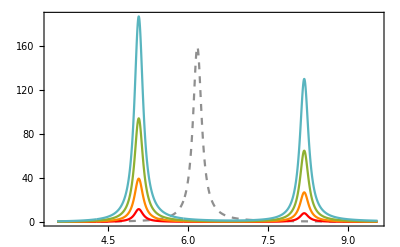

```mathematica
alAR=ListLinePlot[{Style[qextAl3sphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlAR,Red],Style[qextAl1AR,RGBColor[1,0.533,0]],Style[qextAl2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["2\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},Spacings->{0.05},LegendLayout->{"Column",1},LegendLabel->Style[MaTeX["a"],Magnification->1.1]],{0.13,0.65}]]
```

```mathematica
Export["AlAR.svg",alAR]
```

AlAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAlcont=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qscaAlcont=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qextAlcont=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.05}];
qabsAlSph=Table[{h vlight/λ,Cabs[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qscaAlSph=Table[{h vlight/λ,Csca[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
```

```mathematica
h vlight/9
```

137.856

```mathematica
upperTicksAl=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

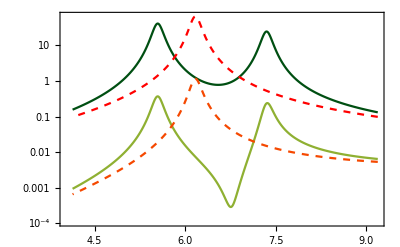

```mathematica
alcont=ListLogPlot[{Style[qabsAlcont,RGBColor[0,0.31,0.071]],Style[qscaAlcont,RGBColor[0.560181,0.691569,0.194885]],Style[qabsAlSph,Dashed,Red],Style[qscaAlSph,Dashed,RGBColor[0.961,0.282,0]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["\mbox{Secciones transversales }[\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.2]&/@{MaTeX["C_{abs}"],MaTeX["C_{sca}"],MaTeX["C_{abs}"],MaTeX["C_{sca}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2}],{0.73,0.15}]]
```

```mathematica
Export["AlContribuciones3.svg",alcont]
```

AlContribuciones3.svg

### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
au=Import["C:\\Users\\Lunita\\OneDrive\\Documentos\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau11=Drop[Drop[au,{51,101}],1];
kau11=Drop[au,{1,52}];
λAu1=nau11[[All,1]]*1000; (*λ en nm*)
nau1=nau11[[All,2]];
kAu1=kau11[[All,2]];
nAu1=nau1+ I kAu1;
aU1=Transpose[{λAu1,nAu1}];
```

```mathematica
nindexau1=Interpolation[aU1];
```

```mathematica
300/(2*Pi*1.33)
```

35.8996

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAu1c=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu2c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu3c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu4c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAuEsferac=Table[{h vlight/λ,Cextexp[2,2,2.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qscaAu4c=Table[{h vlight/λ,Cscaexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,195,1937}];
qabsAu4c=Table[{h vlight/λ,Cabsexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,195,1937}];
```

```mathematica
h vlight/6
```

206.783

```mathematica
upperTicks4=Module[{labels,positions},labels={207,248,310,414,620,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

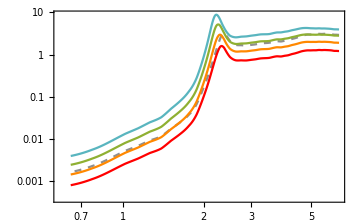

```mathematica
au1c=ListLogLogPlot[{Style[qextAuEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAu1c,Red],Style[qextAu2c,RGBColor[1,0.533,0]],Style[qextAu3c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu4c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} \:[\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.1]],{0.25,0.7}]]
```

```mathematica
Export["Auc.svg",au1c]
```

Auc.svg

```mathematica
N[Log10[10]]
```

1.

#### Misma razón de aspecto

```mathematica
qextAuAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAuEsferaAR=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
```

```mathematica
h c/2
```

1.2407×10^-15

```mathematica
upperTicks4=Module[{labels,positions},labels={207,248,310,414,620,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

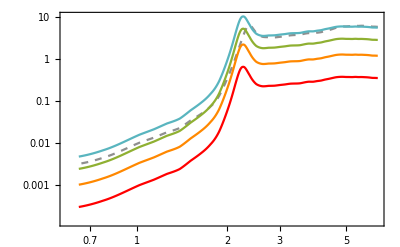

```mathematica
au1AR=ListLogLogPlot[{Style[qextAuEsferaAR,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAuAR,Red],Style[qextAu1AR,RGBColor[1,0.533,0]],Style[qextAu2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.05]&/@{MaTeX["2\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.0,LegendLayout->{"Column",2},LegendLabel->Style[MaTeX["a"],Magnification->1.1]],{0.8,0.25}]]
```

```mathematica
Export["AuAR.svg",au1AR]
```

AuAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAucont=Table[{λ,Cabsexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qscaAucont=Table[{λ,Cscaexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qextAucont=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexau1[λ]]},{λ,300,800}];
```

```mathematica
h vlight/500
```

2.4814

```mathematica
upperTicks4=Module[{labels,positions},labels={0.8,0.85,0.9,0.95,1,1.1,1.2,1.3,1.4,1.5,1.7,2,2.3,2.5,3.1,4};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={0.8,0.85,0.95,1.15,1.25,1.35,1.45,1.55,1.6,1.65,1.75,1.85,2.1,2.3,2.6,2.8};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

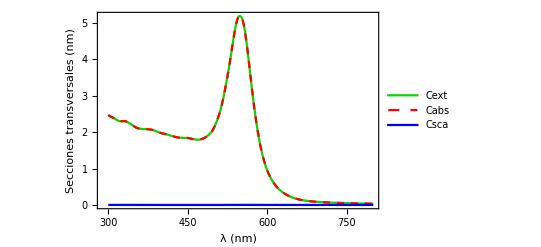

```mathematica
aucont=ListLinePlot[{Style[qextAucont,RGBColor[0.071,0.82,0]],Style[qabsAucont,Red,Dashed],Style[qscaAucont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AuContribuciones1.pdf",aucont]
```

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

#### Oblato

```mathematica
qextAgc=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAgEsferac=Table[{h vlight/λ,Cextexp[2.0,2.0,2.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
```

```mathematica
qabsAg3c=Table[{h vlight/λ,Cabsexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550,0.01}];
qscaAg3c=Table[{h vlight/λ,Cscaexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550,0.01}];
```

```mathematica
h vlight/3.241372910102672
```

382.77

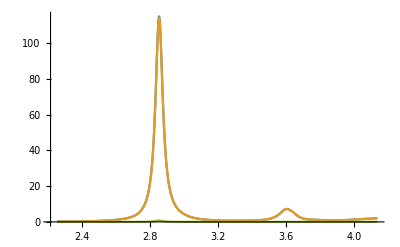

```mathematica
ListLinePlot[{qextAg3c,qabsAg3c,qscaAg3c},PlotRange->All]
```

```mathematica
h vlight/2.5
```

496.28

```mathematica
upperTicksAg=Module[{labels,positions},labels={310,355,414,496};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

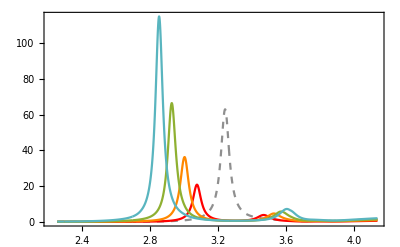

```mathematica
plata1c=ListLinePlot[{Style[qextAgEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgc,Red],Style[qextAg1c,RGBColor[1,0.533,0]],Style[qextAg2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.1]],{0.85,0.65}]]
```

```mathematica
Export["Agc.svg",plata1c]
```

Agc.svg

#### Misma razón de aspecto

```mathematica
qextAgAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,0.75,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
qextAg3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexplata[λ]]},{λ,300,500,0.01}];
```

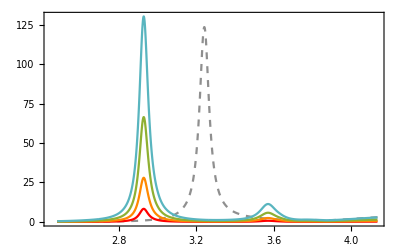

```mathematica
ag1AR=ListLinePlot[{Style[qextAg3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgAR,Red],Style[qextAg1AR,RGBColor[1,0.533,0]],Style[qextAg2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["2.5\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLabel->Style[MaTeX["a"],Magnification->1.1]],{0.85,0.65}]]
```

```mathematica
Export["AgAR.svg",ag1AR]
```

AgAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAgcont=Table[{λ,Cabsexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qscaAgcont=Table[{λ,Cscaexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qextAgcont=Table[{λ,Cextexp[15,15,1,1.33,λ,nindexplata[λ]]},{λ,750,950}];
```

```mathematica
h vlight/950
```

1.306

```mathematica
upperTicksAg=Module[{labels,positions},labels={1.3,1.34,1.37,1.4,1.45,1.5,1.55,1.6,1.65};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={1.31,1.32,1.33,1.35,1.38,1.43,1.48,1.5,1.53,1.63};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

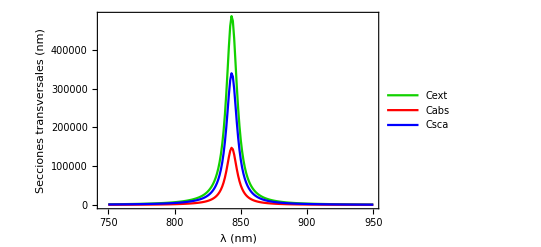

```mathematica
agcont=ListLinePlot[{Style[qextAgcont,RGBColor[0.071,0.82,0]],Style[qabsAgcont,Red],Style[qscaAgcont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AgContribuciones3.pdf",agcont]
```

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
bism=Import["C:\\Users\\Lunita\\OneDrive\\Documentos\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

Import::nffil: File C:\Users\Lunita\OneDrive\Documentos\GitHub\Servicio-Social\Notebooks Mathematica\Funciones dieléctricas\Bismuto Hagemann.csv not found during Import.

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
10/(2*Pi*1.33)
```

1.19665

```mathematica
λBism
```

#### Oblato

```mathematica
qextBic=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBi1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBi2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBi3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
qextBiEsferac=Table[{h vlight/λ,Cextexp[2.25,2.25,2.25,1.33,λ,nindexbismuto[λ]]},{λ,15.5,310}];
```

```mathematica
h vlight/557
```

2.22747

```mathematica
h vlight/8.44014
```

147.

```mathematica
h vlight/0.1
```

12407.

```mathematica
h vlight/50
```

24.814

```mathematica
upperTicksBi=Module[{labels,positions},labels={25,62,124,248};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorBi=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

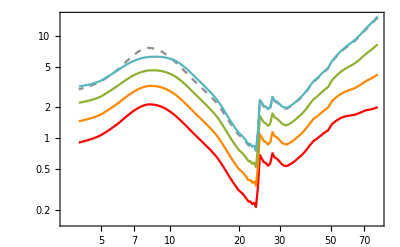

```mathematica
Bismuto1c=ListLogLogPlot[{Style[qextBiEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBic,Red],Style[qextBi1c,RGBColor[1,0.533,0]],Style[qextBi2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.05]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",3},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.1]],{0.23,0.2}]]
```

```mathematica
12.469349837185927-7.649864120216738
```

4.81949

```mathematica
8.644417777077559/2
```

```mathematica
h vlight/4.32221
```

287.052

```mathematica
5.224001300210525
```

```mathematica
h vlight/4.008724745718901-h vlight/23.632386834285715
```

257.

```mathematica
Export["Bic.svg",Bismuto1c]
```

Bic.svg

#### Misma razón de aspecto

```mathematica
qextBiAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
```

```mathematica
h vlight/120
```

10.3392

```mathematica
1.75/2
```

0.875

```mathematica
Graphics[{Pink,Disk[]},PlotRange->{{-.5,.5},{0,1.5}},PlotRangeClipping->True,Frame->True]
```

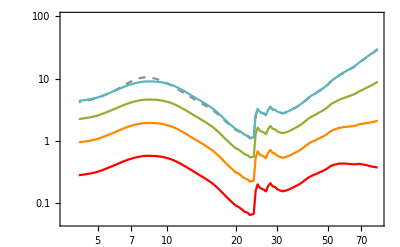

```mathematica
BiAR=ListLogLogPlot[{Style[qextBi3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBiAR,Red],Style[qextBi1AR,RGBColor[1,0.533,0]],Style[qextBi2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext} \:[\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->{0.05,100},Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["2.5\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",5},LegendLabel->Style[MaTeX["a"],Magnification->1.1]],{0.46,0.88}]]
```

```mathematica
Export["BisAR.svg",BiAR]
```

BisAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsBicont=Table[{λ,Cabsexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qscaBicont=Table[{λ,Cscaexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qextBicont=Table[{λ,Cextexp[2,2,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,500}];
```

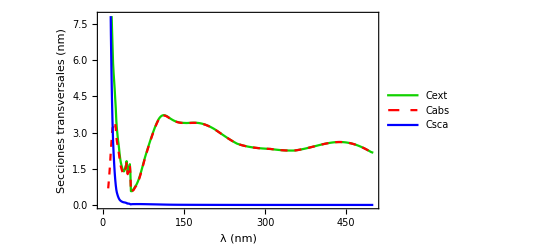

```mathematica
Bismutocont=ListLinePlot[{Style[qextBicont,RGBColor[0.071,0.82,0]],Style[qabsBicont,Red,Dashed],Style[qscaBicont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["BiContribuciones1.pdf",Bismutocont]
```

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

#### Oblato

```mathematica
qextMgOc=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgOcsphere=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
h c/1200
```

1.03392

```mathematica
upperTicksMgO=Module[{labels,positions},labels={1,1.2,1.5,2.1,3.1,6.2};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorMgO=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

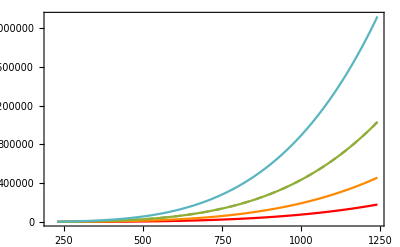

```mathematica
MgO1=ListLinePlot[{Style[qextMgOcsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOc,Red],Style[qextMgO1c,RGBColor[1,0.533,0]],Style[qextMgO2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.05]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",1},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.1]],{0.15,0.6}]]
```

```mathematica
Export["MgOc.svg",MgO1]
```

MgOc.svg

```mathematica
qextMgOAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

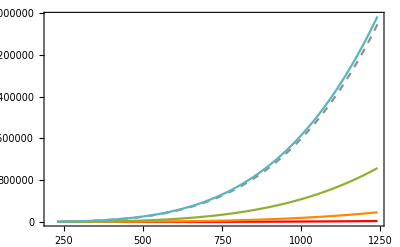

```mathematica
MgO2=ListLinePlot[{Style[qextMgO3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOAR,Red],Style[qextMgO1AR,RGBColor[1,0.533,0]],Style[qextMgO2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.1]&/@{MaTeX["2.5\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",1},LegendLabel->Style[MaTeX["a"],Magnification->1.1]],{0.15,0.6}]]
```

```mathematica
Export["MgOAR.svg",MgO2]
```

MgOAR.svg

## Eritrocitos

```mathematica
RBCreal=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NRealRBC.csv"];
RBCimag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NImagRBC.csv"];
```

```mathematica
λRBC=RBCreal[[All,1]];
nRBC=RBCreal[[All,2]];
kRBC=RBCimag[[All,2]];
nindRBC=nRBC+ I kRBC;
RBC=Transpose[{λRBC,nindRBC}];
```

```mathematica
nindexRBC=Interpolation[RBC];
```

```mathematica
qabsRBC=Table[{λ,Cabsexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qscaRBC=Table[{λ,Cscaexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexp[20,20,12,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpx[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpz[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
```

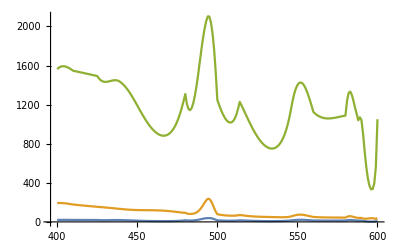

```mathematica
ListLinePlot[{qextRBC,qscaRBC,qabsRBC}]
```

```mathematica
nRBC
```

{1.383,1.365,1.363,1.364,1.365,1.367,1.36481,1.378,1.3728,1.3721,1.361,1.383,1.36053,1.37,1.357,1.3687,1.3668,1.356,1.3667,1.35724,1.356,1.3666}

```mathematica
kRBC
```

{1.4006,1.4007,1.4019,1.404,1.4043,1.4005,1.3993,1.3983,1.3975,1.3973,1.3973,1.3974,1.3974,1.398,1.3978,1.3976,1.3983,1.3975,1.3973,1.39729,1.39728,1.3971}

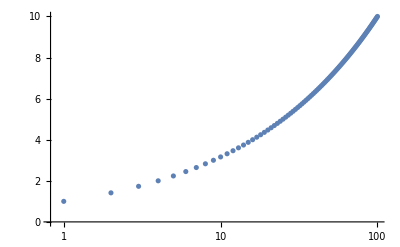

```mathematica
ListLogLinearPlot[Table[{n,Sqrt[n]},{n,100}]]
```

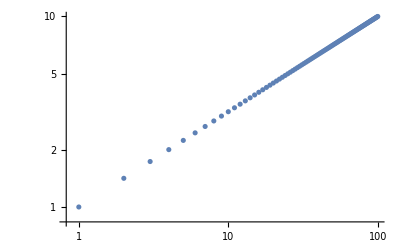

```mathematica
ListLogLogPlot[Table[{n,Sqrt[n]},{n,100}]]
```

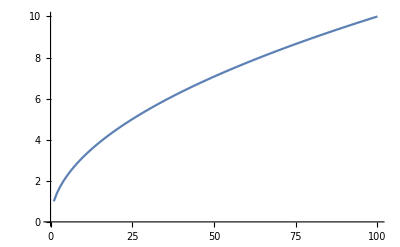

```mathematica
ListLinePlot[Table[{n,Sqrt[n]},{n,100}]]
```